```mathematica
f[r_] = -α  1./r + σ r /. {α-> 0.2, σ-> 3}
```

-0.2/r+3 r

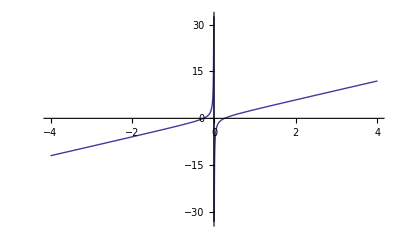

```mathematica
Plot[f[r],{r,-4,4}]
```

```mathematica
fTilde[p_]=4Pi α / p^2 - 8 Pi σ / p^4  /. {α-> 0.2, σ-> 3}
```

2.51327/p^2-(24 π)/p^4

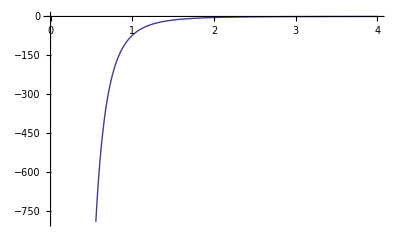

```mathematica
Plot[fTilde[p],{p,0,4}]
```

```mathematica
v[x_,y_,z_] = f[Norm[{x,y,z}]]
```

-0.2/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2))+3 √(Abs[x]^2+Abs[y]^2+Abs[z]^2)

```mathematica
n=40
```

40

```mathematica
vp[x_,y_,z_]=If[
x==0&&y==0&&z==0,
0,
Piecewise[{{v[x,y,z],x≤n/2&&y≤n/2&&z≤n/2},{v[(n-x),y,z],x>n/2&&y≤n/2&&z≤n/2},{v[x,(n-y),z],x≤n/2&&y>n/2&&z≤n/2},{v[x,y,(n-z)],x≤n/2&&y≤n/2&&z>n/2},{v[(n-x),(n-y),z],x>n/2&&y>n/2&&z≤n/2},{v[(n-x),y,(n-z)],x>n/2&&y≤n/2&&z>n/2},{v[x,(n-y),(n-z)],x≤n/2&&y>n/2&&z>n/2},{v[(n-x),(n-y),(n-z)],x>n/2&&y>n/2&&z>n/2}}]]
```

If[x==0&&y==0&&z==0,0,Piecewise[{{v[x,y,z], x≤n/2&&y≤n/2&&z≤n/2}, {v[n-x,y,z], x>n/2&&y≤n/2&&z≤n/2}, {v[x,n-y,z], x≤n/2&&y>n/2&&z≤n/2}, {v[x,y,n-z], x≤n/2&&y≤n/2&&z>n/2}, {v[n-x,n-y,z], x>n/2&&y>n/2&&z≤n/2}, {v[n-x,y,n-z], x>n/2&&y≤n/2&&z>n/2}, {v[x,n-y,n-z], x≤n/2&&y>n/2&&z>n/2}, {v[n-x,n-y,n-z], x>n/2&&y>n/2&&z>n/2}}]]

```mathematica
tab=Table[Sqrt[i*i+j*j+k*k],{i,0,n-1,1},{j,0,n-1,1},{k,0,n-1,1}];
```

```mathematica
ortsraumwerte=Table[vp[i,j,k],{i,0,n-1,1},{j,0,n-1,1},{k,0,n-1,1}];
```

```mathematica
a=0.25
```

0.25

```mathematica
werteFourier = Sqrt[n]^3  * a^2  Fourier[ortsraumwerte];
```

```mathematica
cylinderWerte = Table[werteFourier[[i,j,k]] , {i,2,n-2,1}, {j,i,i+1, 1}, {k,i,i+1,1}];
```

```mathematica
cylinderRadien = Table[(2 Pi / (a n)) * Norm[{i,j,k}], {i,1,n-3,1}, {j,i,i+1, 1}, {k,i,i+1,1}];
```

```mathematica
cylinderPlot = Thread[List[Flatten[cylinderRadien], Flatten[Re[cylinderWerte]]]];
```

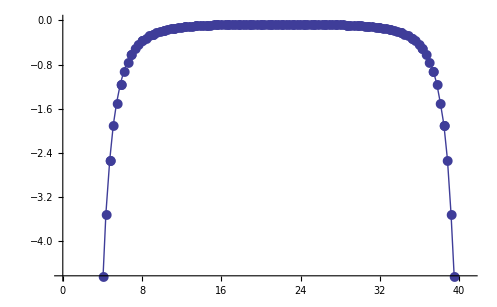

```mathematica
ListLinePlot[cylinderPlot, PlotMarkers->{Automatic, 13}]
```

```mathematica
shift = fTilde[ cylinderPlot[[4,1]] ] - cylinderPlot[[4,2]]
```

95.2083

```mathematica
Manipulate[
ListPlot[{#[[1]], k+ #[[2]]}&/@ cylinderPlot, PlotMarkers->{Automatic, 5},
(*PlotRange-> {{1,10},{-12,1}},*)
Epilog->First@Plot[fTilde[p],{p,0,10}, PlotStyle-> Red]],
{k,0,10}]
```

```mathematica
achsenWerte = Table[{2 Pi / (a n)   Norm[{i,i,i}],werteFourier[[i,i,i]]}, {i,1,n}] // N
```

{{1.08828,230613.},{2.17656,-1110.88},{3.26484,-53.3656},{4.35312,-10.9421},{5.4414,-3.49558},{6.52968,-1.48233},{7.61796,-0.740299},{8.70624,-0.42255},{9.79452,-0.264884},{10.8828,-0.181069},{11.9711,-0.132391},{13.0594,-0.103193},{14.1476,-0.084571},{15.2359,-0.0725664},{16.3242,-0.0644466},{17.4125,-0.0590044},{18.5008,-0.0552214},{19.589,-0.0527157},{20.6773,-0.051057},{21.7656,-0.0501645},{22.8539,-0.0498463},{23.9422,-0.0501645},{25.0304,-0.051057},{26.1187,-0.0527157},{27.207,-0.0552214},{28.2953,-0.0590044},{29.3835,-0.0644466},{30.4718,-0.0725664},{31.5601,-0.084571},{32.6484,-0.103193},{33.7367,-0.132391},{34.8249,-0.181069},{35.9132,-0.264884},{37.0015,-0.42255},{38.0898,-0.740299},{39.1781,-1.48233},{40.2663,-3.49558},{41.3546,-10.9421},{42.4429,-53.3656},{43.5312,-1110.88}}

```mathematica
Manipulate[
ListPlot[{#[[1]], k+ #[[2]]}&/@achsenWerte, PlotMarkers->{Automatic, 5},
(*PlotRange-> {{1,9},{-4,1}},*)
Epilog->First@Plot[fTilde[p],{p,0,10}, PlotStyle-> Red]],
{k,0,10}]
```